## Initialize

```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
SetDirectory[NotebookDirectory[]];

hbar=1.054571800*10^-34;
c=29979245800;
G=6.67408*10^-11;
ρn=2.8*10^14;
phigh2=1.7*10^35;
plow2=5.7*10^34;
phigh6=2.8*10^35;
plow6=7.4*10^34;

pmax=1*10^37;
p0=5.7*10^32;
ϵ0=1.3*10^14;

data=Import["posterior_samples.dat","Data"];
ourγ=Import["../etc/finalSpectralParameters.dat"];
SLy=Drop[Import["../etc/sly.dat","Table"],-30];

SLyPressure=SLy[[All,2]] (c)^2 ;
SLyEnergyDensity=SLy[[All,3]];
SLyMassDensity=SLy[[All,1]];
SLyep=Thread[{SLyMassDensity,SLyPressure}];
SLyrp=Thread[{SLyMassDensity,SLyPressure}];

credible=Drop[Import["../etc/Pressure_density_credible_levels.dat","Data"],1];
MD=10^credible[[All,1]];
P5=10^credible[[All,2]];(*These are the density and pressures at 5/25/75/95 pc*)
P25=10^credible[[All,3]];
P75=10^credible[[All,4]];
P95=10^credible[[All,5]];

grab[a_]:=data[[All,Position[data[[1]],a][[1]][[1]]]]

γ0=Drop[grab["sdgamma0"],1];
γ1=Drop[grab["sdgamma1"],1];
γ2=Drop[grab["sdgamma2"],1];
γ3=Drop[grab["sdgamma3"],1];
γs=Transpose[{γ0,γ1,γ2,γ3}];
logl=Drop[grab["deltalogl"],1];

names=data[[1]];

Γ[γs_,p_]:=Exp[Sum[γs[[k]]*(Log[p/p0])^(k-1),{k,1,Length[γs]}]]; (*Takes γ parameter vector as input*)
μ[γs_,pmax_]:=Exp[-NIntegrate[1/(p*Γ[γs,p]),{p,p0,pmax}]];(*Definition from paper*)
ϵ[γs_,n_]:=Quiet[Table[{(ϵ0+c^-2*NIntegrate[Exp[-NIntegrate[1/(g*Γ[γs,g]),{g,p0,p}]]/Γ[γs,p],{p,p0,y}])/μ[γs,y],y},{y,10^Range[Log10[p0],Log10[pmax],(Log10[pmax]-Log10[p0])/(n-1)]}]];

ρ[ϵ_,ϵList_,pList_]:=ϵList[[1]]*Exp[NIntegrate[1/(Interpolation[Thread[{ϵList,ϵList+pList}]][e]),{e,ϵList[[1]],ϵ}]];
```

## Plot posterior boundaries

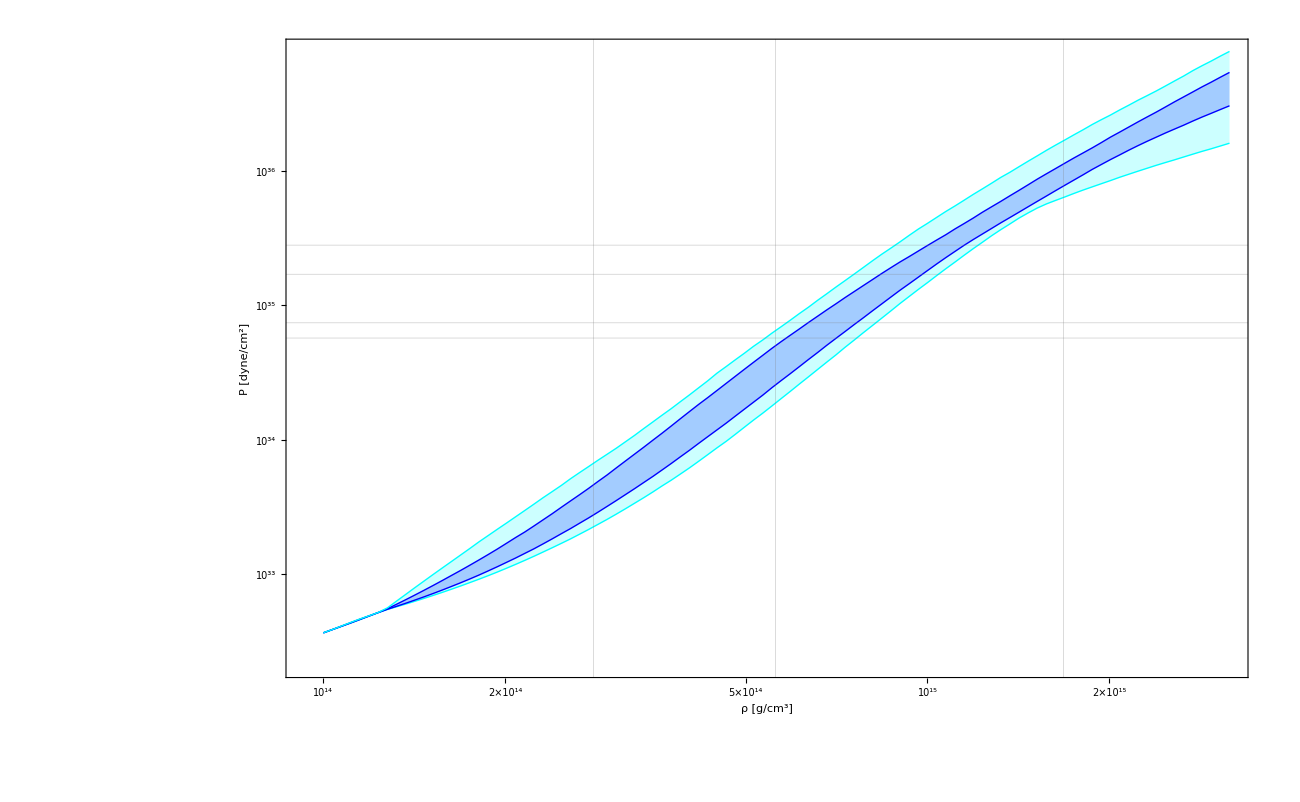

```mathematica
credibleLevels=ListLogLogPlot[{Thread[{MD,P5}],Thread[{MD,P25}],Thread[{MD,P75}],Thread[{MD,P95}]},PlotStyle->{{Thin,Cyan},{Thin,Blue},{Thin,Blue},{Thin,Cyan},Red,Blue,Magenta},Filling->{{1->{4}},{2->{3}}},Joined->True,Frame->True,FrameLabel->{"ρ [g/cm^3]","P [dyne/cm^2]"},BaseStyle->{FontSize->30,FontFamily->"Times"},LabelStyle->Black,GridLines->{{{ρn,{Black,Thick}},{2*ρn,{Black,Thick}},{6*ρn,{Black,Thick}}},{{plow2,{Black,Thick,Dotted}},{phigh2,{Black,Thick,Dotted}},{plow6,{Black,Thick,Dashed}},{phigh6,{Black,Thick,Dashed}}}},ImageSize->1300];

ϵcredibleLevels=ListLogLogPlot[{Thread[{MD,P5}],Thread[{MD,P25}],Thread[{MD,P75}],Thread[{MD,P95}]},PlotStyle->{{Thin,Cyan},{Thin,Blue},{Thin,Blue},{Thin,Cyan},Red,Blue,Magenta},Filling->{{1->{4}},{2->{3}}},Joined->True,Frame->True,FrameLabel->{"ϵ [g/cm^3]","P [dyne/cm^2]"},BaseStyle->{FontSize->30,FontFamily->"Times"},LabelStyle->Black,GridLines->{{{ρn,{Black,Thick}},{2*ρn,{Black,Thick}},{6*ρn,{Black,Thick}}},{{plow2,{Black,Thick,Dotted}},{phigh2,{Black,Thick,Dotted}},{plow6,{Black,Thick,Dashed}},{phigh6,{Black,Thick,Dashed}}}},ImageSize->1300];


SmallcredibleLevels[size_]:=ListLogLogPlot[{Thread[{MD,P5}],Thread[{MD,P25}],Thread[{MD,P75}],Thread[{MD,P95}]},PlotStyle->{{Thin,Cyan},{Thin,Blue},{Thin,Blue},{Thin,Cyan},Red,Blue,Magenta},Filling->{{1->{4}},{2->{3}}},Joined->True,Frame->True,FrameLabel->{"ρ [g/cm^3]","P [dyne/cm^2]"},BaseStyle->{FontSize->30,FontFamily->"Times"},LabelStyle->Black,GridLines->{{{ρn,{Black,Thick}},{2*ρn,{Black,Thick}},{6*ρn,{Black,Thick}}},{{plow2,{Black,Thick,Dotted}},{phigh2,{Black,Thick,Dotted}},{plow6,{Black,Thick,Dashed}},{phigh6,{Black,Thick,Dashed}}}},ImageSize->size];

PlotList[list_]:=ListLogLogPlot[list,Joined->True,Frame->True,FrameLabel->{"ρ[g/cm^3]","P [dyne/cm^2]"},BaseStyle->{FontSize->20,FontFamily->"Times"},LabelStyle->Black,ImageSize->600];

NumberedPlotList[list_,num_]:=ListLogLogPlot[list,Joined->True,Frame->True,FrameLabel->{"ρ [g/cm^3]","P [dyne/cm^2]"},PlotStyle->Red,BaseStyle->{FontSize->20,FontFamily->"Times"},LabelStyle->Black,ImageSize->600,PlotLegends->{Placed[LineLegend[{"Spectral EoS "<>ToString[num]},LabelStyle->{Bold,FontSize->28},LegendFunction->"Frame"],{Left,Top}]}];
credibleLevels
```

## Look at parameters

-Graphics-

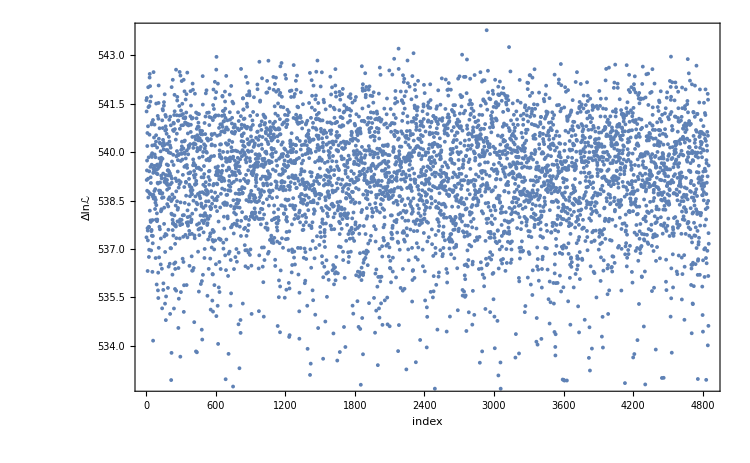

```mathematica
ListPlot[{Thread[{γ2,γ3}],Thread[{ourγ[[All,3]],ourγ[[All,4]]}]},PlotMarkers->{".","*"},Frame->True,FrameLabel->{"γ_2","γ_3"},ImageSize->750,BaseStyle->{FontSize->30,FontFamily->"Times"},LabelStyle->Black]

ListPlot[logl,Frame->True,FrameLabel->{"index","Δlnℒ"},ImageSize->750,BaseStyle->{FontSize->30,FontFamily->"Times"},LabelStyle->Black]
```

## Generate 100 EoSs

## Randomly pick 100

```mathematica
(*num=Length[γ1];
ran=Sort[RandomSample[Range[num],100]];*)
ran=Import["EoSs/randomNumbers.dat","List"];
```

```mathematica
ℒ=Part[logl,ran];
γ=Thread[{Part[γ0,ran],Part[γ1,ran],Part[γ2,ran],Part[γ3,ran]}];

ListPlot[{Thread[{γ2,γ3}],Thread[{ourγ[[All,3]],ourγ[[All,4]]}],Thread[{γ[[All,3]],γ[[All,4]]}]},PlotMarkers->{".","*","*"},Frame->True,FrameLabel->{"γ_2","γ_3"},ImageSize->750,BaseStyle->{FontSize->30,FontFamily->"Times"},LabelStyle->Black]

ListPlot[{logl,Thread[{ran,ℒ}]},Frame->True,FrameLabel->{"index","Δlnℒ"},ImageSize->750,PlotMarkers->{".","*"},BaseStyle->{FontSize->30,FontFamily->"Times"},LabelStyle->Black]
```

-Graphics-

-Graphics-

## Generate EoSs

```mathematica
(*bleh=Timing[ϵ[γ[[1]],100]];
{bleh[[1]]*Length[γ]/3600," Hours"}*)
```

```mathematica
(*p=100;
ep=ConstantArray[0,Length[γ]];
rp=ConstantArray[{},Length[γ]];
stitchedrp=ConstantArray[{},Length[γ]];
stitchedep=ConstantArray[{},Length[γ]];

For[i=0,i<Length[γ],i++;{
Print["Working on Full integration, EoS "<>ToString[i]<>" of "<>ToString[Length[γ]]<>"..."],
ep[[i]]=ϵ[γ[[i]],p];

ϵlist=ep[[i]][[All,1]];
plist=ep[[i]][[All,2]]/c^2;
For[j=0,j<Length[ϵlist],j++;AppendTo[rp[[i]],{ρ[ϵlist[[j]],ϵlist,plist],plist[[j]]*c^2}]];

stitchedrp[[i]]=Join[SLyrp,rp[[i]]];
stitchedep[[i]]=Join[SLyep,ep[[i]]];

Export["EoSs/ep/eos"<>ToString[i]<>".dat",stitchedep[[i]],"TSV"];
Export["EoSs/rp/eos"<>ToString[i]<>".dat",stitchedrp[[i]],"TSV"];
Export["EoSs/tov_ready/eos"<>ToString[i]<>".dat",Transpose[{ConstantArray[1,Length[stitchedep[[i]]]],1/c^2 stitchedep[[i]][[All,2]],stitchedep[[i]][[All,1]]}],"TSV"];
}]

Show[credibleLevels,PlotList[stitchedrp]]
Show[credibleLevels,PlotList[stitchedep]]
*)
```

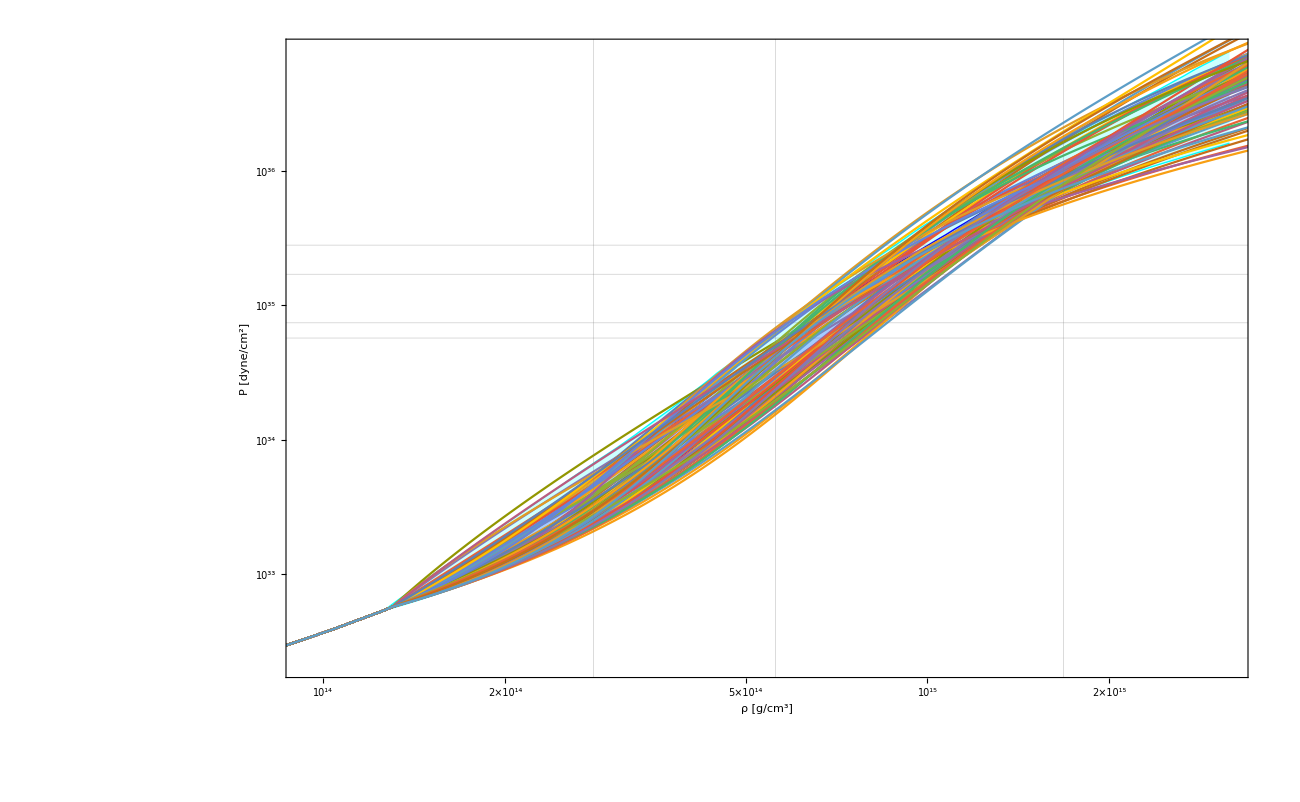

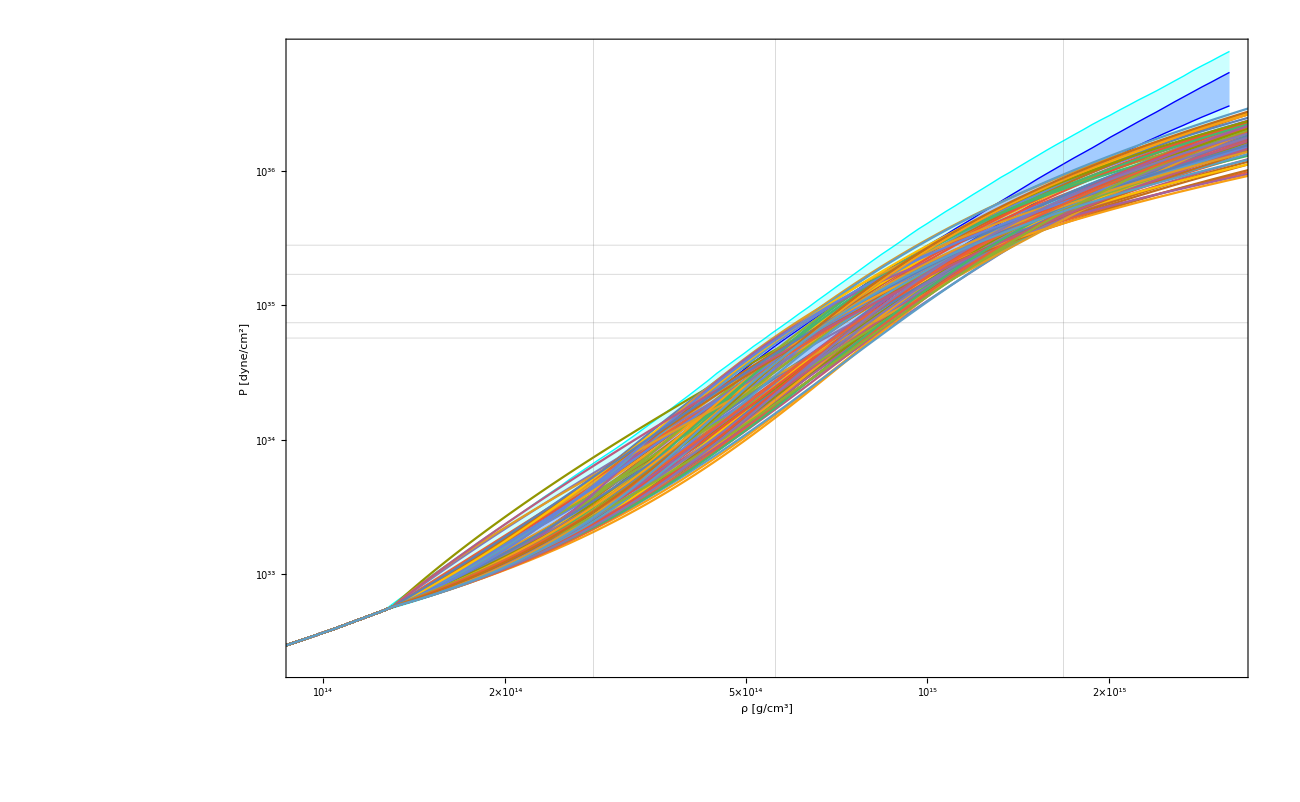

```mathematica
stitchedrp=Delete[stitchedrp,{{43},{11},{3}}];
stitchedep=Delete[stitchedep,{{43},{11},{3}}];

Show[credibleLevels,PlotList[stitchedrp]]
Show[credibleLevels,PlotList[stitchedep]]
```

## Export to XMGrace

```mathematica
(*For[i=0,i<35,i++;
Export["../../paper/XMgrace/EoSs/PosteriorEoS"<>ToString[i]<>".dat",AppendTo[stitchedrp[[i]],{}]];
]*)
```

## Import and plot EoSs if already generated

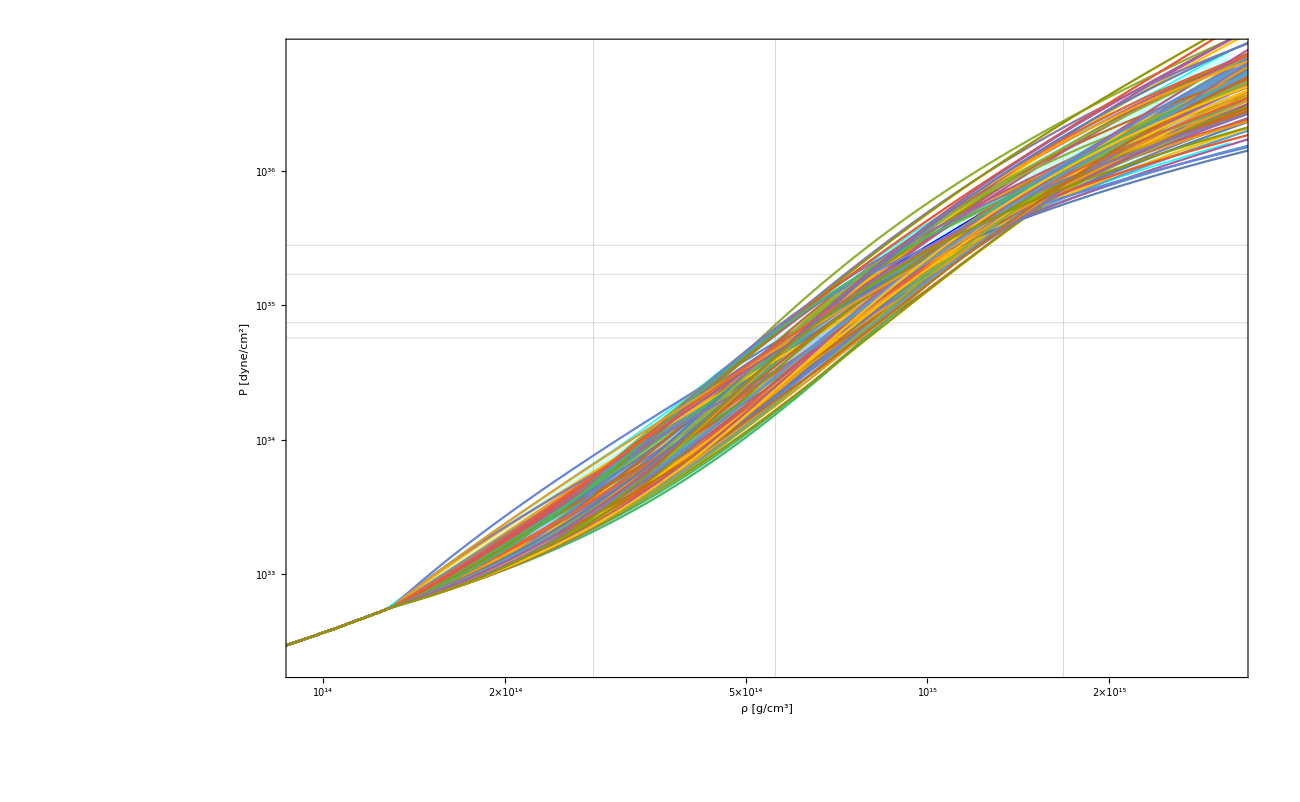

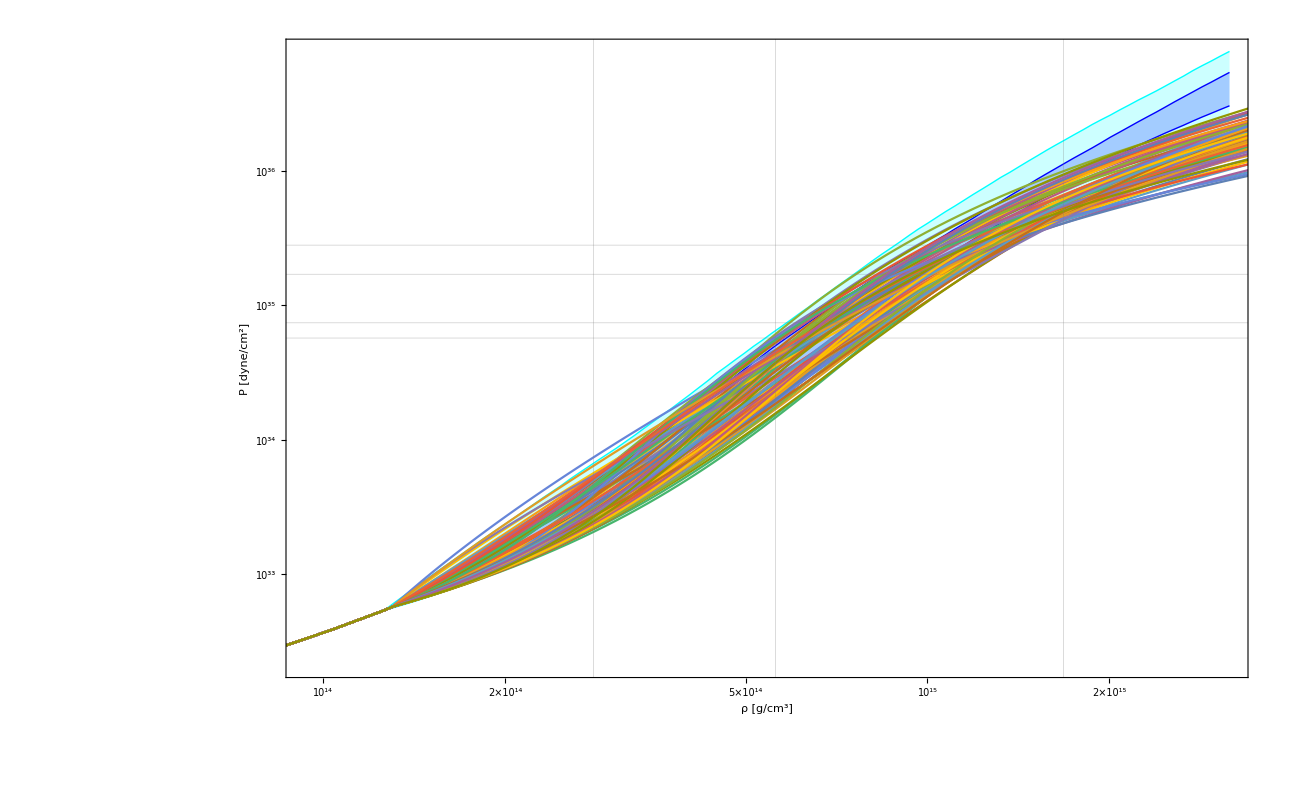

```mathematica
stitchedrp=ConstantArray[{},Length[γ]];
stitchedep=ConstantArray[{},Length[γ]];
For[i=0,i<Length[γ],i++;
stitchedrp[[i]]=Import["EoSs/rp/eos"<>ToString[i]<>".dat"];
stitchedep[[i]]=Import["EoSs/ep/eos"<>ToString[i]<>".dat"];
]
Show[credibleLevels,PlotList[stitchedrp]]
Show[credibleLevels,PlotList[stitchedep]]
```